# P3HT / O-IDTBR Charge-Transfer Exciton Model

## Companion code for: Jindal, Janik & Milner, "First-Principles Modeling of Interfacial Charge Transfer Exciton States in Organic Solar Cells" (JCTC).

## Overview

This notebook orchestrates the full calculation of charge-transfer (CT) exciton energies at a P3HT / O-IDTBR donor-acceptor interface, using a tight-binding model parameterized from DFT and applied to close-contact geometries taken from a molecular dynamics trajectory.

The total CT exciton energy is E_CT = E_K + E_C + E_P, i.e. the one-body kinetic energy of the delocalized electron and hole (E_K), the electron-hole Coulomb interaction (E_C), and the dielectric polarization stabilization (E_P) (Eq. 2 and Eq. 12 of the paper).

Evaluate sections in order from top to bottom.

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

## Importing molecular configurations

This block imports one MD frame (npt.gro), parses atom lists for P3HT and IDTBR, and converts coordinates from nm to Angstrom for the energy model.

Importing molecular configurations from a single frame of molecular dynamics simulation

```mathematica
importFrame[fName_]:=Module[{},
frame=Import[fName,"Table"];
nAtoms=frame[[2,1]];
lBox3D=10 frame[[-1]];
(*Importing P3HT 24-mers(128)*)
atoms1=frame[[3;;10001,{2,4,5,6}]];
atoms2=frame[[10002;;33794,{2,3,4,5}]];
atoms=Join[atoms1,atoms2];
atoms[[All,2;;-1]]*=10;
newNames=Flatten[Table[{"CA","CA","CA","CA","S","C2","C2","C2","C2","C2","C2"},128*24]];
atoms[[All,1]]=newNames;
(*Importing IDTBR molecules (300)*)
idtbrAtoms=frame[[33795;;-2,{2,3,4,5}]];
idtbrAtoms[[All,2;;-1]]*=10;
idtbrNames=Flatten[Table[{"C","C","N","S","C","C","S","O","C","C","C","C","C","C","C","N","N","S","C","C","C","C","S","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","C","S","C","C","C","C","C","C","C","C","C","N","N","S","C","S","C","O","N","C","C","C","S","C","C","C","C","C","C","C","C","C","C","C","C","C","C"},300]];
idtbrAtoms[[All,1]]=idtbrNames;
{lBox3D,atoms,idtbrAtoms}
]
```

Importing Data from .gro (IDTBR-P3HT interface from MD simulations done on GROMACS) which contains 128 P3HT chains and 300 IDTBR molecules in a PBC box

```mathematica
{pbc3D,atomP3HT,atomIDTBR}=importFrame["data/npt.gro"];
```

## Finding ring centers and close-contacts between IDTBR & P3HT

Ring centers are constructed under periodic boundary conditions, then BT-thiophene close contacts are filtered to define interface pairs used by all later calculations.

Atoms of the kth ring in a P3HT melt (assuming 11 atoms per monomer)

```mathematica
p3htAtoms[k_]:=atomP3HT[[11(k-1)+1;;11(k-1)+5]][[All,2;;-1]]
rh1Atoms[k_]:=atomIDTBR[[88(k-1)+1;;88(k-1)+5]][[All,2;;-1]]
btd1Atoms[k_]:=atomIDTBR[[88(k-1)+10;;88(k-1)+15]][[All,2;;-1]]
idt1Atoms[k_]:=atomIDTBR[[88(k-1)+19;;88(k-1)+23]][[All,2;;-1]]
idbAtoms[k_]:=atomIDTBR[[{88(k-1)+24,88(k-1)+25,88(k-1)+27,88(k-1)+44,88(k-1)+45,88(k-1)+47}]][[All,2;;-1]]
rh2Atoms[k_]:=atomIDTBR[[{88(k-1)+66,88(k-1)+67,88(k-1)+68,88(k-1)+70,88(k-1)+71}]][[All,2;;-1]]
btd2Atoms[k_]:=atomIDTBR[[88(k-1)+56;;88(k-1)+61]][[All,2;;-1]]
idt2Atoms[k_]:=atomIDTBR[[{88(k-1)+48,88(k-1)+50,88(k-1)+53,88(k-1)+54,88(k-1)+55}]][[All,2;;-1]]
```

PBC functions

```mathematica
pbc[r_]:=Mod[r,pbc3D];
dpbc[dr_]:=Mod[dr,pbc3D,-pbc3D/2];
nearestImage[r0_,r_]:=r0+dpbc[r-r0];
```

Finding center of ring given the list of atoms in the ring

```mathematica
ringCenter[atomList_]:=Module[{},
posns=atomList;
newPosns=nearestImage[posns[[1]],#]&/@posns;
pbc[Mean[newPosns]]
]
```

#### Finding center of rings (in P3HT and BTD in IDTBR)

```mathematica
ccListP3HT = Array[ringCenter[p3htAtoms[#]]&, 128*24];
```

```mathematica
ccListBTD1= Array[ringCenter[btd1Atoms[#]]&, 300];
ccListBTD2= Array[ringCenter[btd2Atoms[#]]&, 300];
```

```mathematica
ccListBTD=Join[ccListBTD1,ccListBTD2];
```

```mathematica
plot3D=Graphics3D[{(*Smaller points for Thiophene (P3HT)*)
Style[Point[ccListP3HT],PointSize[Small], Red],
(*Larger points for Benzothiadiazole (BTD)*)
Style[Point[ccListBTD],PointSize[Medium], Blue]},
Boxed->True,Axes->True,AxesLabel->{"X","Y","Z"},
PlotRange->{{0,pbc3D[[1]]},{0,pbc3D[[2]]},{0,pbc3D[[3]]}}]
```

-Graphics3D-

Chain # from ring #

```mathematica
nChain[k_]:=Ceiling[k/24]
```

Boolean function identifying chain ends

```mathematica
isEnd[k_]:=If[Mod[k,24,1]==1||Mod[k,24,1]==24,True,False]
```

Finding close-contacts

```mathematica
(*Function to find close contacts between Thiophene and BTD rings*)
findCloseContacts[k_,max_]:=Module[{thiopheneCenter,closeBTDs,indexPairs},
(*Get the center of the current Thiophene ring*)
thiopheneCenter=ccListP3HT[[k]];
(*Find BTD rings within the cutoff distance*)
closeBTDs=Position[ccListBTD,#]&/@Select[ccListBTD,Norm[dpbc[#-thiopheneCenter]]<=max&]//Flatten;
(*Generate index pairs (Thiophene index,BTD index)*)
indexPairs={k,#}&/@closeBTDs;
(*Return the index pairs*)
indexPairs];
```

```mathematica
(*Find all close contacts for Thiophene-BTD rings within a cutoff of 5 units*)
ThioBTDcloseContacts=Array[findCloseContacts[#,5.]&,Length[ccListP3HT]];
(*Flatten the list of close contacts to remove empty entries*)
ThioBTDcloseContacts=DeleteCases[Flatten[ThioBTDcloseContacts,1],{}];
```

```mathematica
ThioBTDpairList=Select[ThioBTDcloseContacts,!(isEnd[#[[1]]]||isEnd[#[[1]]-2]||isEnd[#[[1]]+2])&];
```

```mathematica
Length[ThioBTDpairList]
```

237

#### Function to calculate close contact pair {p3ht, idtbr} to get molecular geometries

```mathematica
GetCloseContactRingPair[i_]:=Module[{ThioNo,BTDno,IDTBRno},
{ThioNo,BTDno}=ThioBTDpairList[[i]];
IDTBRno=If[BTDno>300,BTDno-300,BTDno];
{ThioNo, IDTBRno}
];
```

#### Function to calculate close contact BTD geometry to get interchain hopping term

```mathematica
btdAtoms[i_]:=Module[{ThioNo,BTDno},
{ThioNo,BTDno}=ThioBTDpairList[[i]];
If[BTDno>300,btd2Atoms[BTDno-300],btd1Atoms[BTDno]]
];
```

```mathematica
thioAtoms[i_]:=p3htAtoms[ThioBTDpairList[[i,1]]];
```

Visualize the contact pairs along with P3HT and IDTBR chain segments

```mathematica
drawInterfaceContact[n_]:=Module[{mid1,mid2},
{mid1,mid2}=GetCloseContactRingPair[n];
ringCenter[p3htAtoms[mid1]];
ListPointPlot3D[{
Table[nearestImage[ringCenter[idbAtoms[mid2]],#]&/@p3htAtoms[i],{i,mid1-3,mid1+3}]//Flatten[#,1]&,
rh1Atoms[mid2],
btd1Atoms[mid2],
idt1Atoms[mid2],
idbAtoms[mid2],
idt2Atoms[mid2],
btd2Atoms[mid2],
rh2Atoms[mid2]
},(*PlotRange->{{0,pbc3D[[1]]},{0,pbc3D[[2]]},{0,pbc3D[[3]]}},*)BoxRatios->Automatic,PlotStyle->{Orange,Cyan,Green,Cyan,Cyan,Cyan,Green,Cyan}]]
```

### Interaction Matrix

This subsection builds the smeared Gaussian Coulomb kernel for the 14-site CT basis. It is reused in total Coulomb and polarization energy evaluations.

Smeared Coulomb interaction

```mathematica
IDTBRringsCenter[n_]:={ringCenter[rh1Atoms[n]],
ringCenter[btd1Atoms[n]],
ringCenter[idt1Atoms[n]],
ringCenter[idbAtoms[n]],
ringCenter[idt2Atoms[n]],
ringCenter[btd2Atoms[n]],
ringCenter[rh2Atoms[n]]};
```

```mathematica
getCloseContactPosn[nThpair_]:=Module[{a,b,seg1,seg2},
{a,b}=GetCloseContactRingPair[nThpair];
seg1=Table[ringCenter[p3htAtoms[i]],{i,a-3,a+3}];
seg2=IDTBRringsCenter[b];
Join[seg1,seg2]
]
```

```mathematica
eps=3.0;
eFac=27.2*0.529;  (*for distance in angstroms*) 
deltaP3HT=Table[4.,{7}];
deltaIDTBR={6.,4.4,4.,4.15,4.,4.4,6.};
deltaCT=Join[deltaP3HT,deltaIDTBR];(*Size of monomer units (in order) for P3HT-IDTBR system*)
```

```mathematica
matCoulIntCT[posns_]:=Module[{mat},
mat=eFac Outer[0&,posns,posns,1];
Do[If[i!=j,mat[[i,j]]=eFac/Norm[dpbc[posns[[i]]-posns[[j]]]]*Erf[Norm[dpbc[posns[[i]]-posns[[j]]]]/((deltaCT[[i]]+deltaCT[[j]])/2)]],{i,14},{j,14}];
Do[mat[[i,i]]=eFac/(Sqrt[Pi](deltaCT[[i]]/2)),{i,14}];
mat
]
```

### Getting Intra-chain hopping terms

DFT-derived monomer/dimer energies are imported here and converted to intrachain hopping distributions for P3HT and IDTBR bond types.

```mathematica
ThDimerGS=Import["data/energies_extracted/ThDimer_gsE.txt","Table"];
ThDimerCation=Import["data/energies_extracted/Unrestricted/Cation_ThDimer.txt","Table"];
ThDimerAnion=Import["data/energies_extracted/Unrestricted/Anion_ThDimer.txt","Table"];
RhBT1GS=Import["data/energies_extracted/RhBT1_gsE.txt","Table"];
RhBT1Cation=Import["data/energies_extracted/Unrestricted/cations/RhBT1_cationU.txt","Table"];
RhBT1Anion=Import["data/energies_extracted/Unrestricted/anions/RhBT1_anionU.txt","Table"];
RhBT2GS=Import["data/energies_extracted/RhBT2_gsE.txt","Table"];
RhBT2Cation=Import["data/energies_extracted/Unrestricted/cations/RhBT2_cationU.txt","Table"];
RhBT2Anion=Import["data/energies_extracted/Unrestricted/anions/RhBT2_anionU.txt","Table"];
ThBT1GS=Import["data/energies_extracted/ThBT1_gsE.txt","Table"];
ThBT1Cation=Import["data/energies_extracted/Unrestricted/cations/ThBTD1_cationU.txt","Table"];
ThBT1Anion=Import["data/energies_extracted/Unrestricted/anions/ThBTD1_anionU.txt","Table"];
ThBT2GS=Import["data/energies_extracted/ThBT2_gsE.txt","Table"];
ThBT2Cation=Import["data/energies_extracted/Unrestricted/cations/ThBTD2_cationU.txt","Table"];
ThBT2Anion=Import["data/energies_extracted/Unrestricted/anions/ThBTD2_anionU.txt","Table"];
```

#### Formatting

```mathematica
ThDimerGS=ThDimerGS[[All,1]];
ThDimerCation=ThDimerCation[[All,1]];
ThDimerAnion=ThDimerAnion[[All,1]];
```

```mathematica
ThBT1GS=ThBT1GS[[All,1]];
ThBT1Cation=ThBT1Cation[[All,1]];
ThBT1Anion=ThBT1Anion[[All,1]];
ThBT2GS=ThBT2GS[[All,1]];
ThBT2Cation=ThBT2Cation[[All,1]];
ThBT2Anion=ThBT2Anion[[All,1]];
```

```mathematica
RhBT1GS=RhBT1GS[[All,1]];
RhBT1Cation=RhBT1Cation[[All,1]]; 
RhBT1Anion=RhBT1Anion[[All,1]];
RhBT2GS=RhBT2GS[[All,1]];
RhBT2Cation=RhBT2Cation[[All,1]];
RhBT2Anion=RhBT2Anion[[All,1]];
```

#### Monomer cation, anion energies (B3LYP wo RO)

Optimized Geometry B3LYP

```mathematica
{BenAnion,BenCation,BenGS}={-232.227630711,-231.959359844,-232.297902709};
{ThAnion,ThCation,ThGS}={-552.999105696,-552.735570737,-553.061979360};
{BTDAnion,BTDCation,BTDGS}={-738.836969934,-738.491016167,-738.814871833};
{RhAnion,RhCation,RhGS}={-1159.38182101,-1159.02889428,-1159.34861317};
```

```mathematica
fac=27.2114;
{eCationBen,eAnionBen}=fac{ BenCation-BenGS,BenAnion-BenGS};
{eCationThio,eAnionThio}=fac{ ThCation-ThGS,ThAnion-ThGS};
{eCationBTD,eAnionBTD}=fac{ BTDCation-BTDGS,BTDAnion-BTDGS};
{eCationRh,eAnionRh}=fac{ RhCation-RhGS,RhAnion-RhGS};
```

```mathematica
Dimer cation, anion energies
```

```mathematica
eCationP3HT=fac(ThDimerCation-ThDimerGS);
eAnionP3HT=fac(ThDimerAnion-ThDimerGS);
```

```mathematica
ringNums=Select[Range[128*24],(Mod[#,24]!=0)&];
```

```mathematica
eCationThBT=fac Join[ThBT1Cation-ThBT1GS,ThBT2Cation-ThBT2GS];
eAnionThBT=fac Join[ThBT1Anion-ThBT1GS,ThBT2Anion-ThBT2GS];
```

```mathematica
eCationRhBT=fac Join[RhBT1Cation-RhBT1GS,RhBT2Cation-RhBT2GS];
eAnionRhBT=fac Join[RhBT1Anion-RhBT1GS,RhBT2Anion-RhBT2GS];
```

#### Function to get hopping term between two monomer

```mathematica
tDist[eA_,eB_,eABdist_]:=Module[{dE},
dE=eA+eB-2eABdist;
Sqrt[dE^2- (eA-eB)^2]/2
];
```

IDT is bridged three monomer entity, the bond between Thio-Ben is thus planar

```mathematica
pOptAnion=fac(-784.147882137+784.166171694);
pOptCation=fac(-783.881088822+784.166171694);
tHoleThBen=tDist[eCationThio,eCationBen,pOptCation];
tElecThBen=tDist[eAnionThio,eAnionBen,pOptAnion];
```

Rh-BT is free to rotate, the hopping term between Rh-BT does not vary much

```mathematica
tHoleRhBT=tDist[eCationRh,eCationBTD,eCationRhBT];
```

### Figure 5: Distribution of intrachain hopping matrix elements for IDTBR:

### (b) hole hopping between benzothiadiazole and rhodanine (t^h_BTRh),

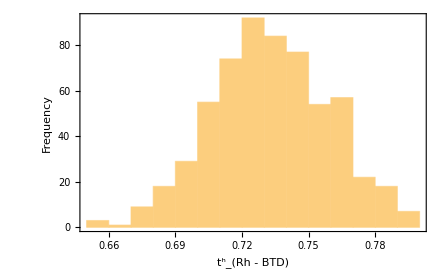

```mathematica
Histogram[tHoleRhBT,Frame->True,FrameLabel->{"(t^h)_(Rh - BTD)","Frequency"}]
```

### (d) electron hopping between benzothiadiazole and rhodanine ((t^e)_(BT Rh)).

```mathematica
tElecRhBT=tDist[eAnionRh,eAnionBTD,eAnionRhBT];
```

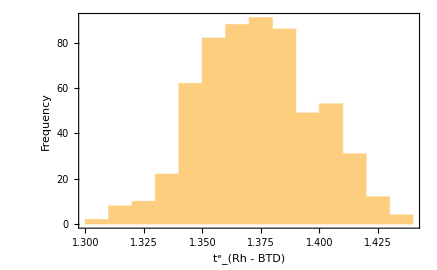

```mathematica
Histogram[tElecRhBT,Frame->True,FrameLabel->{"(t^e)_(Rh - BTD)","Frequency"}]
```

Th-BT is also free to rotate, the variation in the hopping terms between Th-BT is large

### (c) electron hopping between thiophene and benzothiadiazole ((t^e)_(Th BT)),

```mathematica
tElecThBT=tDist[eAnionThio,eAnionBTD,eAnionThBT];
```

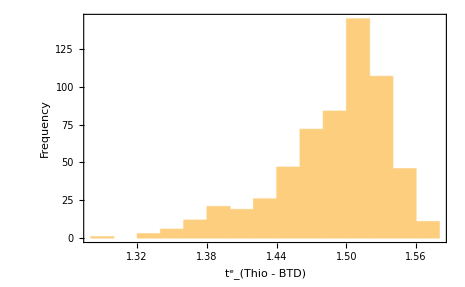

```mathematica
Histogram[tElecThBT, Frame->True,FrameLabel->{"(t^e)_(Thio - BTD)","Frequency"}]
```

### (a) hole hopping between thiophene and benzothiadiazole (t^h _ThBT )

```mathematica
tHoleThBT=tDist[eCationThio,eCationBTD,eCationThBT];
```

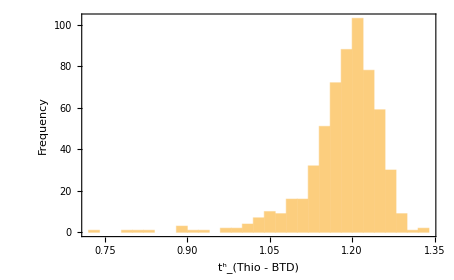

```mathematica
Histogram[tHoleThBT,Frame->True,FrameLabel->{"(t^h)_(Thio - BTD)","Frequency"}]
```

### Hopping Matrix Element for Polythiophene (P3HT)

In P3HT, the hopping terms between adjacent thiophene monomers are significantly different because of the dihedral disorder

#### Figure 4: Distribution of intrachain hopping matrix elements along P3HT

```mathematica
tHoleP3HT=tDist[eCationThio,eCationThio,eCationP3HT];
```

### (a) hole transport ((t^h)_Th)

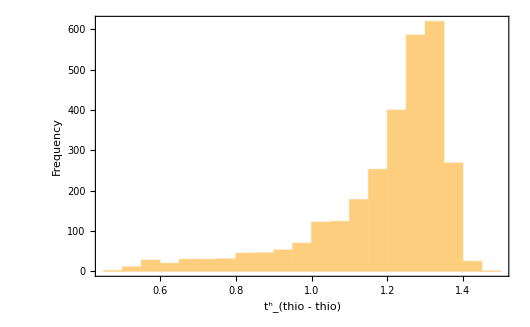

```mathematica
Histogram[tHoleP3HT[[ringNums]],Frame->True,FrameLabel->{"(t^h)_(thio - thio)","Frequency"}]
```

```mathematica
tElecP3HT=tDist[eAnionThio,eAnionThio,eAnionP3HT];
```

### (b) electron transport ((t^e)_Th)

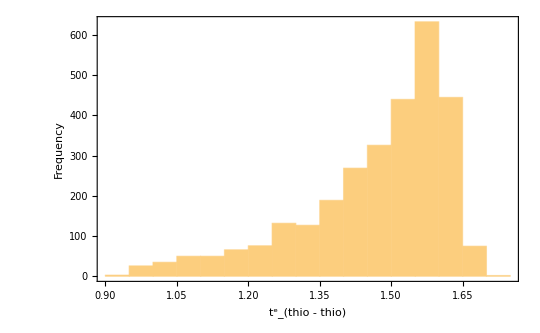

```mathematica
Histogram[tElecP3HT[[ringNums]],Frame->True,FrameLabel->{"(t^e)_(thio - thio)","Frequency"}]
```

### P3HT and IDTBR (Parameters, Hamiltonian, Interaction Matrix)

This part assembles onsite energies, hopping vectors, and helper objects for constructing hole/electron Hamiltonians on the 14-site donor-acceptor manifold.

P3HT - containing seven thiophenes, and IDTBR  with close contact at the middle thiophene of P3HT and left BT of IDTBR, perpendicular to each other, and rotated by angle theta and separated by a distance z

### Gathering Hopping Terms

tHoleP3HT, tElecP3HT --> monomer-wise hopping term for all thio-thio pairs in P3HT
tHoleRhBTD, tHoleThBTD, tHoleThBen (constant)

```mathematica
tHoleRhBTleft=tHoleRhBT[[1;;300]];
tHoleRhBTright=tHoleRhBT[[301;;600]];
tHoleThBTleft=tHoleThBT[[1;;300]];
tHoleThBTright=tHoleThBT[[301;;600]];
```

tElecRhBTD, tElecThBTD, tElecThBen (constant)

```mathematica
tElecRhBTleft=tElecRhBT[[1;;300]];
tElecRhBTright=tElecRhBT[[301;;600]];
tElecThBTleft=tElecThBT[[1;;300]];
tElecThBTright=tElecThBT[[301;;600]];
```

### Parameters

Parameters for thiophene/P3HT

```mathematica
eH=Table[-eCationThio,{i,7}]; (*Onsite energy for HOMO*)
eL=Table[eAnionThio,{7}]; (*Onsite energy for LUMO*)
tH[i_]:=Table[-tHoleP3HT[[k]],{k,i-3,i+2}]; (*Hopping terms for HOMO*)
tL[i_]:=Table[-tElecP3HT[[k]],{k,i-3,i+2}];  (*Hopping terms for LUMO*)
VcP3HT=Table[4.717,{7}];  (*Onsite Coul. energy term for monomers*)
Vcidtbr={3.854,4.309,4.717,4.914,4.717,4.309,3.854}; 
VcCT=Join[VcP3HT,Vcidtbr];
```

Parameters for IDTBR

```mathematica
tInterchain=Import["data/predictedt600.csv"]//Flatten;
```

### Figure 6: Distribution of inter chain hopping matrix elements (t_ab) between P3HT and OIDTBR close contacts in a well-equilibrated amorphous P3HT:IDTBR blend.

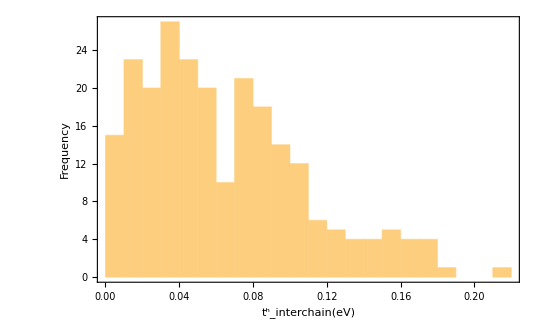

```mathematica
Histogram[tInterchain,{0.01},Frame->True,FrameLabel->{"(t^h)_interchain(eV)","Frequency"}]
```

### Figure 6: Distribution of interchain hopping matrix elements (tab) between P3HT and OIDTBR close contacts in a well-equilibrated amorphous P3HT:IDTBR blend.

```mathematica
eHidtbr=-{eCationRh,eCationBTD,eCationThio,eCationBen,eCationThio,eCationBTD,eCationRh}; (*Onsite energy for HOMO*)
eLidtbr={eAnionRh,eAnionBTD,eAnionThio,eAnionBen,eAnionThio,eAnionBTD,eAnionRh}; (*Onsite energy for LUMO*)
tHidtbr[i_]:=-{tHoleRhBTleft[[i]],tHoleThBTleft[[i]],tHoleThBen,tHoleThBen,tHoleThBTright[[i]],tHoleRhBTright[[i]]};  (*Hopping terms for HOMO*)
tLidtbr[i_]:={tElecRhBTleft[[i]],tElecThBTleft[[i]],tElecThBen,tElecThBen,tElecThBTright[[i]],tElecRhBTright[[i]]};   (*Hopping terms for LUMO*)
t12[kthPair_]:=tInterchain[[kthPair]];
```

### Getting initial condition

Getting smeared Coulomb interaction matrix for initial and final polaron state calculations

```mathematica
getCloseContactPosn[nThpair_]:=Module[{a,b,seg1,seg2},
{a,b}=GetCloseContactRingPair[nThpair];
seg1=Table[ringCenter[p3htAtoms[i]],{i,a-3,a+3}];
seg2=IDTBRringsCenter[b];
Join[seg1,seg2]
]
```

```mathematica
sig=2.0;
uCs[r_]:=Erf[r/(2 sig)]/r;
uCs[0]:=1/(Sqrt[Pi]sig);
uCs[0.]:=1/(Sqrt[Pi]sig);
```

```mathematica
getIntP3HT[nThpair_]:=Module[{seg},
seg=getCloseContactPosn[nThpair][[1;;7]];
eFac Outer[uCs[Norm[dpbc[#1-#2]]]&,seg,seg,1]
]
```

```mathematica
getIntIDTBR[nThpair_]:=Module[{mat},
posns=getCloseContactPosn[nThpair][[8;;14]];
mat=eFac Outer[0&,posns,posns,1];
Do[If[i!=j,mat[[i,j]]=eFac/Norm[dpbc[posns[[i]]-posns[[j]]]]*Erf[Norm[dpbc[posns[[i]]-posns[[j]]]]/((deltaIDTBR[[i]]+deltaIDTBR[[j]])/2)]],{i,7},{j,7}];
Do[mat[[i,i]]=eFac/(Sqrt[Pi](deltaIDTBR[[i]]/2)),{i,7}];
mat
]
```

Polaron hopping and stabilization energy

```mathematica
ePol[psiL_,tL_,int_]:=Module[{psi,qVals},
psi=psiL/Norm[psiL];
qVals=psi^2;
-2Total[tL psi[[1;;-2]]psi[[2;;-1]] ]-(1/2)(1-1/eps)qVals.int.qVals]
```

```mathematica
psi0={0.02,0.164,0.4468,0.7359,0.4468,0.164,0.02};
```

```mathematica
ePolMin[psiL_,tL_,int_]:=Module[{arg,guess},
psi0=psiL/Norm[psiL];
arg=Array[psi,7];
guess=Transpose[{arg,psi0}];
FindMinimum[{ePol[arg,tL,int],arg.arg==1},guess]
]
```

```mathematica
holePolP3HT[nThpair_]:=Module[{p3ht,idtbr},
{p3ht,idtbr}=GetCloseContactRingPair[nThpair];
ePolMin[psi0,tH[p3ht],getIntP3HT[nThpair]]
]
```

```mathematica
wv7mer=Table[psi[i],{i,7}];
```

```mathematica
elecPolIDTBR[nThpair_]:=Module[{p3ht,idtbr},
{p3ht,idtbr}=GetCloseContactRingPair[nThpair];
ePolMin[psi0,tLidtbr[idtbr],getIntIDTBR[nThpair]]
];
```

#### Hamiltonian Matrix

Hamiltonian for P3HT 7-mer and IDTBR molecules in close contact at center moiety of P3HT and BT (2nd monomer) in IDTBR

```mathematica
elemCTLeft[i_,j_,e1_,e2_,t1_,t2_,t12_,n1_,n2_]:=Which[
i==j&&i<=n1,e1[[i]],
(j==i+1)&&i<n1,-t1[[i]],
(j==i-1)&&i<=n1,-t1[[j]],
i==j&&n1<i<=n1+n2,e2[[i-n1]],
(j==i+1)&&n1<i<n1+n2,-t2[[i-n1]],
(j==i-1)&&n1+1<i<=n1+n2,-t2[[j-n1]],
(i==Ceiling[n1/2])&&(j==n1+2),-t12,
(j==Ceiling[n1/2])&&(i==n1+2),-t12,
True,0]
```

```mathematica
elemCTRight[i_,j_,e1_,e2_,t1_,t2_,t12_,n1_,n2_]:=Which[
i==j&&i<=n1,e1[[i]],
(j==i+1)&&i<n1,-t1[[i]],
(j==i-1)&&i<=n1,-t1[[j]],
i==j&&n1<i<=n1+n2,e2[[i-n1]],
(j==i+1)&&n1<i<n1+n2,-t2[[i-n1]],
(j==i-1)&&n1+1<i<=n1+n2,-t2[[j-n1]],
(i==Ceiling[n1/2])&&(j==n1+6),-t12,
(j==Ceiling[n1/2])&&(i==n1+6),-t12,
True,0]
```

Putting together a Hamiltonian Matrix for CT exciton

```mathematica
elemCT[i_,j_,e1_,t1_]:=Which[
i==j&&i<=n1,e1[[i]],
(j==i+1)&&i<n1,-t1[[i]],
(j==i-1)&&i<=n1,-t1[[j]],
True,0]
```

```mathematica
matCTp3ht[e1_,t1_]:=Array[elemCT[#1,#2,e1,t1]&,{7,7}]
```

#### function to calculate close contact pair {p3ht, idtbr} to get molecular geometries

```mathematica
GetCloseContactRingPair[i_]:=Module[{ThioNo,BTDno,IDTBRno},
{ThioNo,BTDno}=ThioBTDpairList[[i]];
IDTBRno=If[BTDno>300,BTDno-300,BTDno];
{ThioNo, IDTBRno}
];
```

```mathematica
GetRightorLeft[i_]:=Module[{ThioNo,BTDno},
{ThioNo,BTDno}=ThioBTDpairList[[i]];
If[BTDno>300,2,1]
]
```

```mathematica
matCTexciton[RorL_,eP3HT_,eIDTBR_,tP3HT_,tIDTBR_,tCloseContact_]:=If[RorL==2,Array[elemCTRight[#1,#2,eP3HT,eIDTBR,tP3HT,tIDTBR,tCloseContact,7,7]&,{14,14}],If[RorL==1,Array[elemCTLeft[#1,#2,eP3HT,eIDTBR,tP3HT,tIDTBR,tCloseContact,7,7]&,{14,14}]]]
```

```mathematica
n1=Length[eH];
n2=Length[eHidtbr];
```

### CT exciton at P3HT/IDTBR interface

The total CT exciton energy functional is defined and minimized per contact. Final outputs include CT energies, decomposition into one-body and interaction terms, and trend/outlier analysis.

#### Setting up total CT exciton energy

```mathematica
Clear[matKEelecCT,matKEholeCT,intmat,CTexctionE];
```

Hamiltonian for hole at close-contact, i

```mathematica
matKEholeCT[i_]:=matCTexciton[GetRightorLeft[i],eH,eHidtbr,tH[GetCloseContactRingPair[i][[1]]],tHidtbr[GetCloseContactRingPair[i][[2]]],-t12[i]];
```

Hamiltonian for electron at contact

```mathematica
matKEelecCT[i_]:=matCTexciton[GetRightorLeft[i],eL,eLidtbr,tL[GetCloseContactRingPair[i][[1]]],tLidtbr[GetCloseContactRingPair[i][[2]]],t12[i]];
```

Interaction matrix for CT exciton

```mathematica
intmat[i_]:=matCoulIntCT[getCloseContactPosn[i]];
```

Total CT exciton energy = Total Kinetic E + Coulomb E + Polarization E

```mathematica
CTexctionE[psiE_,psiH_,i_]:=Module[{qElec,qHole,qNet,eKE,eCoul,ePolz},
qElec=-(psiE^2); (* -ve charge distt*)
qHole=psiH^2; (* +ve charge distrution*)
qNet=qHole+qElec;  (* total charge distribution*)
eKE= (psiE.matKEelecCT[i].psiE) - (psiH.matKEholeCT[i].psiH); (* electron KE + hole KE *)
eCoul=(qElec).intmat[i].(qHole)+(VcCT-eFac/(Sqrt[Pi](deltaCT/2))).(qElec qHole); 
(* offsite coulomb E + onsite correction term*)
ePolz=qNet.(-1/2(1-1/eps)intmat[i]).qNet; (*polarization E due to total charge distribution*)
eKE+eCoul+ePolz (*Total exction energy*)
]
```

#### Getting charge transfer exciton for all close-contact pairs

Fitting polaron on P3HT and IDTBR and using them to find CT exciton

```mathematica
(* electron on entirely on IDTBR*)
psiEfull = {0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.3,0.4,0.2,0.1,0.2,0.4,0.3}/0.76857;
(* hole entirely on P3HT 7-mer *)
psiHfull = {0.2,0.3,0.4,0.5,0.4,0.3,0.2,0.01,0.01,0.01,0.01,0.01,0.01,0.01}/0.9114;
```

Separated CT exciton

```mathematica
CTexctionMin2[psiE0_,psiH0_,k_]:=Module[{},
psiEG=psiE0/Norm[psiE0];
psiHG=psiH0/Norm[psiH0];
argsE=Table[psiE[i],{i,1,14}];
argsH=Table[psiH[i],{i,1,14}];
guessElec=Transpose[{argsE,psiEG}];
guessHole=Transpose[{argsH,psiHG}];
guesses=Join[guessElec,guessHole];
holeONp3ht=Sum[argsH[[i]]^2,{i,1,7}];
elecONidtbr=Sum[argsE[[i]]^2,{i,8,14}];
FindMinimum[{CTexctionE[argsE,argsH,k],argsE.argsE==1.,argsH.argsH==1.,elecONidtbr>0.999,holeONp3ht>0.999},guesses]
](*CT exciton separated version*)
```

```mathematica
CTexcitonEnergyList=Table[CTexctionMin2[psiEfull,psiHfull,kthPair][[1]],{kthPair,1,237}];
```

### Figure 9: Energy distribution of CT exciton across all P3HT-IDTBR close contacts.

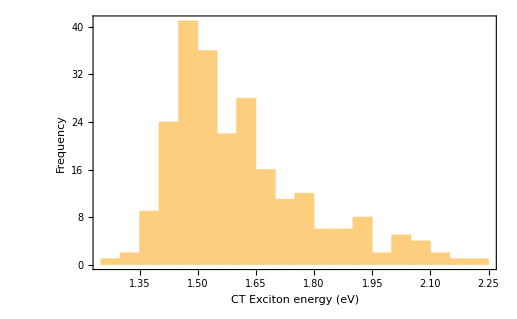

```mathematica
Histogram[CTexcitonEnergyList,{0.05},Frame->True, FrameLabel->{"CT Exciton energy (eV)","Frequency"} ]
```

Exciton on IDTBR

```mathematica
CTexctionMin3[psiE0_,psiH0_,k_]:=Module[{},
psiEG=psiE0/Norm[psiE0];
psiHG=psiH0/Norm[psiH0];
argsE=Table[psiE[i],{i,1,14}];
argsH=Table[psiH[i],{i,1,14}];
guessElec=Transpose[{argsE,psiEG}];
guessHole=Transpose[{argsH,psiHG}];
guesses=Join[guessElec,guessHole];
holeONibtbr=Sum[argsH[[i]]^2,{i,8,14}];
elecONidtbr=Sum[argsE[[i]]^2,{i,8,14}];
FindMinimum[{CTexctionE[argsE,argsH,k],argsE.argsE==1.,argsH.argsH==1.,elecONidtbr==1. ,holeONibtbr==1.},guesses]
](* exciton on IDTBR version*)
```

```mathematica
zero7={0,0,0,0,0,0,0};
```

```mathematica
IDTBRexcitonEnergyList=Table[CTexctionMin3[Join[zero7,wv7mer/.elecPolIDTBR[kthPair][[2]]],Join[zero7,wv7mer/.holePolP3HT[kthPair][[2]]],kthPair][[1]],{kthPair,1,237}];
```

Figure 8: Energy distribution of exciton localized on IDTBR across all P3HT-IDTBR close contacts

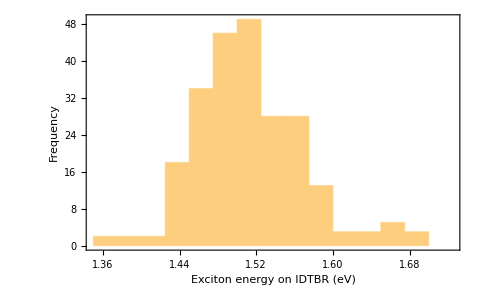

```mathematica
Histogram[IDTBRexcitonEnergyList,{0.025},Frame->True, FrameLabel->{"Exciton energy on IDTBR (eV)","Frequency"} ]
```

### Figure 10: Scatter plot comparing CT exciton energy and IDTBR exciton energy for each donor–acceptor configuration. The red dashed line indicates equal energy.

```mathematica
min=Min[Min[CTexcitonEnergyList],Min[IDTBRexcitonEnergyList]];
max=Max[Max[CTexcitonEnergyList],Max[IDTBRexcitonEnergyList]];
```

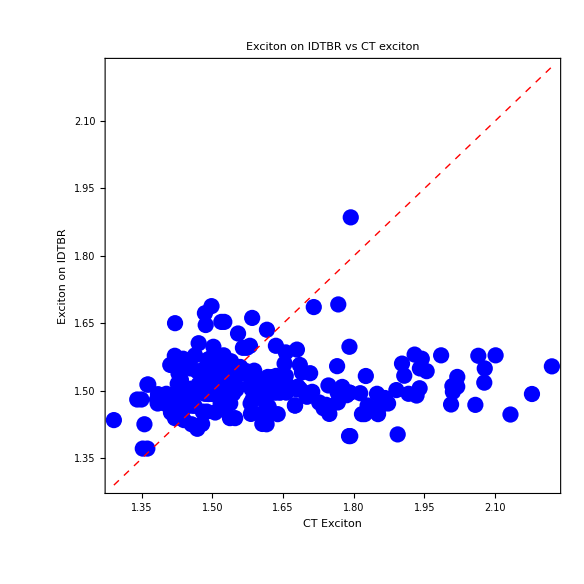

```mathematica
ListPlot[Transpose[{CTexcitonEnergyList,IDTBRexcitonEnergyList}],
PlotStyle->{PointSize[0.02],Blue},FrameLabel->{"CT Exciton","Exciton on IDTBR"},PlotLabel->"Exciton on IDTBR vs CT exciton",Epilog->{Red,Dashed,Line[{{min,min},{max,max}}]},
PlotRange->{{min,max},{min,max}},AspectRatio->1]
```

#### Low-energy CT state

1. A scatter plot, of the computed CT state energy, versus the sum of the two one-body energies (i.e., the electron and hole separately, with no Coulomb term, and no medium polarization term).  This tests the idea is that “straight chains make good CT states”, and the sum of the one-body energies is an indicator of how straight the chains are.  

2. A scatter plot of the computed CT state energy, versus the Coulomb energy (electron-hole interaction, plus medium polarization energy).  This tests the alternative idea that “strong Coulomb attraction makes good CT states”.

Total CT exciton energy = Total Kinetic E + Coulomb E + Polarization E

```mathematica
CTSolve[k_]:=Module[{res,sol,psiEopt,psiHopt,qElec,qHole,qNet,eCoulOpt,ePolzOpt,eKEOpt,holeKE,elecKE},
psiEG=psiEfull/Norm[psiEfull];
psiHG=psiHfull/Norm[psiHfull];
argsE=Table[psiE[i],{i,1,14}];
argsH=Table[psiH[i],{i,1,14}];
guessElec=Transpose[{argsE,psiEG}];
guessHole=Transpose[{argsH,psiHG}];
guesses=Join[guessElec,guessHole];
holeONp3ht=Sum[argsH[[i]]^2,{i,1,7}];
elecONidtbr=Sum[argsE[[i]]^2,{i,8,14}];res=FindMinimum[{CTexctionE[argsE,argsH,k],argsE.argsE==1,argsH.argsH==1,elecONidtbr>0.999,holeONp3ht>0.999},guesses];
sol=res[[2]];
psiEopt=argsE/. sol;
psiHopt=argsH/. sol;
eKEOpt= (psiEopt.matKEelecCT[k].psiEopt) - (psiHopt.matKEholeCT[k].psiHopt); 
elecKE =(psiEopt.matKEelecCT[k].psiEopt) ;
holeKE =- (psiHopt.matKEholeCT[k].psiHopt);
qElec=-(psiEopt^2);
qHole=psiHopt^2;
qNet=qHole+qElec;
eCoulOpt=(qElec).intmat[k].(qHole)+(VcCT-eFac/(Sqrt[Pi] (deltaCT/2))).(qElec qHole);
ePolzOpt=qNet.(-1/2 (1-1/eps) intmat[k]).qNet;
{res[[1]],eCoulOpt+ePolzOpt,eKEOpt,eCoulOpt,ePolzOpt,elecKE,holeKE,psiEopt,psiHopt}]
```

```mathematica
results=Table[CTSolve[k],{k,1,237}];
CTexcitonE=results[[All,1]];
OneBodyE=results[[All,3]];
CoulombE=results[[All,2]];
```

```mathematica
lm=LinearModelFit[Transpose[{OneBodyE,CTexcitonE}],x,x];
residuals=CTexcitonE-lm/@OneBodyE;
```

#### Cleaning Data

```mathematica
rho=StandardDeviation[residuals];
keepIdx=Flatten@Position[Abs[residuals],_?(#<=1.8*rho&)];
RemoveIds=Flatten@Position[Abs[residuals],_?(#>1.8*rho&)];
```

```mathematica
lm2=LinearModelFit[Transpose[{OneBodyE[[keepIdx]],CTexcitonE[[keepIdx]]}],x,x];
residuals2=CTexcitonE[[keepIdx]]-lm2/@OneBodyE[[keepIdx]];
```

#### Outlier Analysis

{Coulomb, Polarization, Coulomb + Pol Energy}

```mathematica
{Mean[results[[All,4]][[keepIdx]]],Mean[results[[All,5]][[keepIdx]]],Mean[results[[All,2]][[keepIdx]]]}
```

{-2.31395,-0.426919,-2.74087}

Outliers

```mathematica
{Mean[results[[All,4]][[RemoveIds]]],Mean[results[[All,5]][[RemoveIds]]],Mean[results[[All,2]][[RemoveIds]]]}
```

{-0.946818,-1.29698,-2.2438}

{Electron KE, Hole KE, Total KE}

```mathematica
{Mean[results[[All,6]][[keepIdx]]],Mean[results[[All,7]][[keepIdx]]],Mean[results[[All,3]][[keepIdx]]]}
```

{-2.40411,6.71497,4.31086}

Outliers

```mathematica
{Mean[results[[All,6]][[RemoveIds]]],Mean[results[[All,7]][[RemoveIds]]],Mean[results[[All,3]][[RemoveIds]]]}
```

{-2.41352,6.66276,4.24924}

### Figure 11: CT exciton energy versus sum of one-body kinetic energies of electron and hole in CT state (E_(1b)) for all P3HT–IDTBR interfaces.

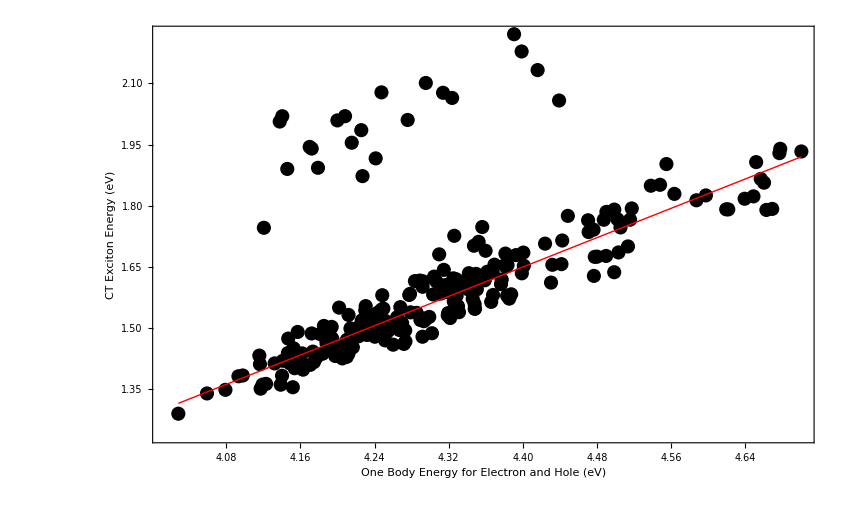

```mathematica
Show[ListPlot[Transpose[{OneBodyE,CTexcitonE}],
PlotStyle->{PointSize[0.012],Black},FrameLabel->{"One Body Energy for Electron and Hole (eV)","CT Exciton Energy (eV)"}],Plot[lm2[x],{x,Min[OneBodyE],Max[OneBodyE]},PlotStyle->{Red,Thick}]]
```

### Figure 12: CT exciton energy versus Coulomb+polarization interaction energy for all P3HT–IDTBR interfaces.

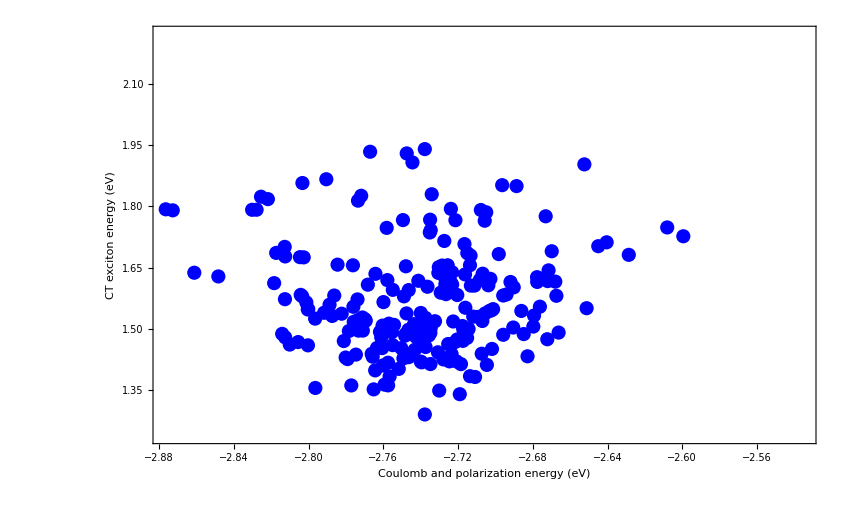

```mathematica
ListPlot[results[[All,{2,1}]],Frame->True,PlotStyle->{PointSize[0.012],Blue},FrameLabel->{"Coulomb and polarization energy (eV)","CT exciton energy (eV)"}]
```

#### Outlier Analysis

### Table 3: Mean Coulomb, polarization, and total interaction energies for CT excitons on the main one-body trendline and for outlier configurations.

{Coulomb, Polarization, Coulomb + Pol Energy}

```mathematica
{Mean[results[[All,4]][[keepIdx]]],Mean[results[[All,5]][[keepIdx]]],Mean[results[[All,2]][[keepIdx]]]}
```

{-2.31395,-0.426919,-2.74087}

Outliers

```mathematica
{Mean[results[[All,4]][[RemoveIds]]],Mean[results[[All,5]][[RemoveIds]]],Mean[results[[All,2]][[RemoveIds]]]}
```

{-0.946818,-1.29698,-2.2438}

{Electron KE, Hole KE, Total KE}

```mathematica
{Mean[results[[All,6]][[keepIdx]]],Mean[results[[All,7]][[keepIdx]]],Mean[results[[All,3]][[keepIdx]]]}
```

{-2.40411,6.71497,4.31086}

Outliers

```mathematica
{Mean[results[[All,6]][[RemoveIds]]],Mean[results[[All,7]][[RemoveIds]]],Mean[results[[All,3]][[RemoveIds]]]}
```

{-2.41352,6.66276,4.24924}

### Figure 13: Residual CT exciton energy (deviation from the best-fit one-body trend) versus Coulomb+polarization interaction energy, after excluding outliers.

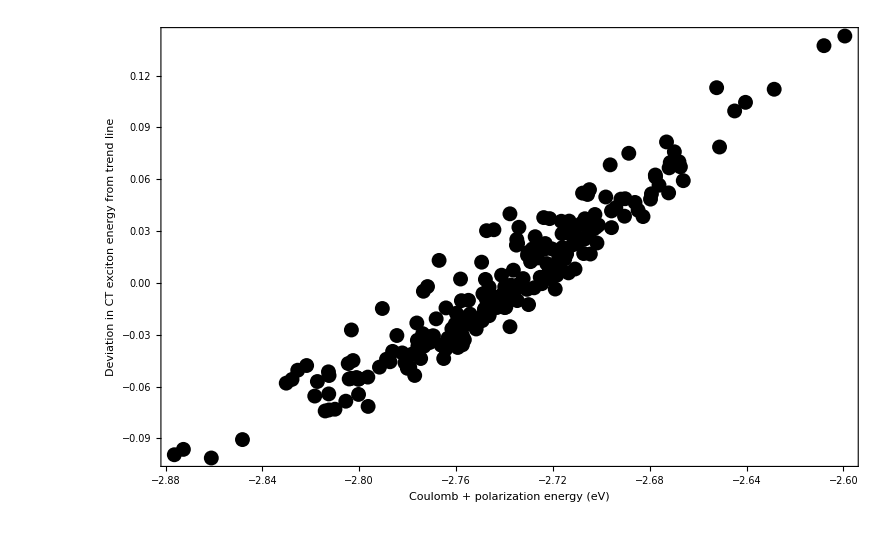

```mathematica
ListPlot[Transpose[{CoulombE[[keepIdx]],residuals2}],PlotStyle->{PointSize[0.012],Black},Frame->True,FrameLabel->{"Coulomb + polarization energy (eV)","Deviation in CT exciton energy from trend line"}]
```